```mathematica
rawList =ReadList["/home/mjmchugh/Mott/MottG4/CrossSections/Mott-DWBA-Au-5MeV.out",{Number,Number,Number,Number,Number}];
```

```mathematica
Geant4AD=ReadList["/home/mjmchugh/Mott/MottG4/CrossSections/G4AngularDistribution.dat",{Number,Number}];
```

```mathematica
Geant4CS=ReadList["/home/mjmchugh/Mott/MottG4/CrossSections/G4InterpolatedCrossSection.dat",{Number,Number}];
```

```mathematica
Theta= Table[rawList[[i]][[1]],{i,1,427}];
CrossSection = Table[rawList[[i]][[2]],{i,1,427}];
Sherman = Table[rawList[[i]][[5]],{i,1,427}];
ThetaDist=Table[Geant4AD[[i]][[1]],{i,1,1000}];
PhiDist=Table[Geant4AD[[i]][[2]],{i,1,1000}];
```

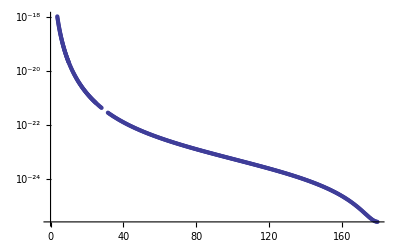

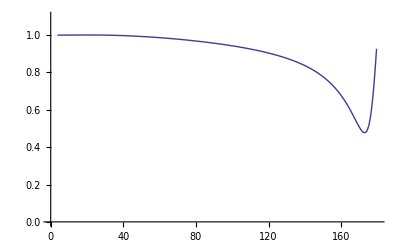

```mathematica
ListLogPlot[Table[{Theta[[i]],CrossSection[[i]]},{i,1,427}]]
ListLinePlot[Table[{Theta[[i]],1+Sherman[[i]]},{i,1,427}],PlotRange->{{-.1,180},{0.0,1.1}},Axes->True]
```

```mathematica
CSS=Table[{Theta[[i]],CrossSection[[i]]*(1-Sherman[[i]])},{i,1,427}];
CS=Table[{Theta[[i]],CrossSection[[i]]},{i,1,427}];
```

```mathematica
CSFunk =Interpolation[CS,InterpolationOrder->1]
CSSFunk =Interpolation[CSS,InterpolationOrder->1]
```

InterpolatingFunction[{{3.7,179.5}},<>]

InterpolatingFunction[{{3.7,179.5}},<>]

```mathematica
CSFunk[172]
CSSFunk[172]
```

5.5716×10^-26

8.46011×10^-26

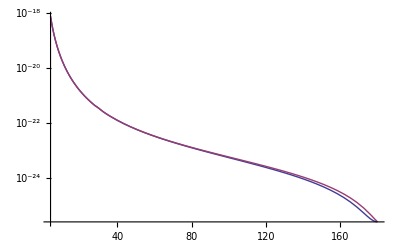

```mathematica
LogPlot[{CSFunk[θ],CSSFunk[θ]},{θ,4,180}]
```

```mathematica
diff= Table[{Geant4CS[[i]][[1]],2*(Geant4CS[[i]][[2]]-CSFunk[Geant4CS[[i]][[1]]])/(Geant4CS[[i]][[2]]+CSFunk[Geant4CS[[i]][[1]]])},{i,1,1100}];
```

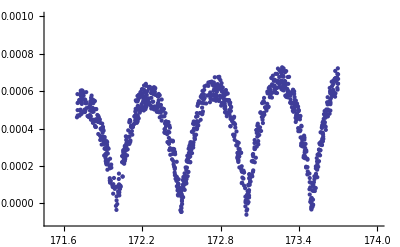

```mathematica
ListPlot[diff,PlotRange->{{171.5,174.0},{-0.0001,0.001}}]
```

```mathematica
Mean[diff]
```

{172.71,0.000402483}

```mathematica
StandardDeviation[diff]
```

{0.576151,0.000187158}

```mathematica
360/(2π)0.192/2.850
```

3.85993

```mathematica
2.850/Tan[7.4*π/180]
```

21.9438

```mathematica
x = 2.85/(2Tan[7.4*π/180])
```

10.9719

```mathematica
ArcTan[1.329/x]*180/π
```

6.90646

```mathematica
ArcTan[1.521/x]*180/π
```

7.89244

```mathematica
180-6.9
```

173.1

```mathematica
180-7.9
```

172.1

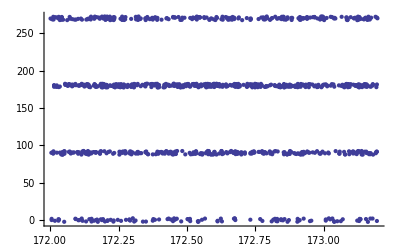

```mathematica
ListPlot[Geant4AD]
```

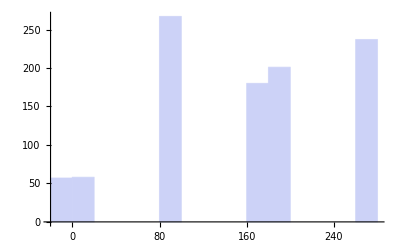

```mathematica
Histogram[PhiDist]
```